# A Boolean model of geroconversion

Loading the library

```mathematica
$Path = $Path  ∪ {NotebookDirectory[]};
```

```mathematica
<<Booned`
```

```mathematica
Clear[TF, F, nodes, istates, states, nextstate, randomValues,n, simulation, ig0]
```

#### Transition function

```mathematica
TF = {
   Insulin -> Insulin,
   GF -> GF,
   Senescence ->  (! p16 && p21 && mTORC1S6K1) || (p16),
   G1S -> (! p21 && CDK2 && E2F1 && Metabolism),
   MAPK -> (GF && ! PP2A),
   p16 -> (MAPK && ! p53 && ! E2F1 && ! PRC),
   MDM2 -> (! p16 && ! p53 && AKT && ! mTORC1S6K1 && ! MYC && ! E2F1) || (! p16 && p53 && ! mTORC1S6K1 && ! MYC && ! E2F1) || (p16 && ! mTORC1S6K1 && ! MYC && ! E2F1),
   p53 -> (! MDM2),
   p21 -> (! p53 && ! AKT && ! MYC && FOXO) || (p53 && ! AKT && ! MYC),
   AKT -> (! IRSPIK3CA && ! PTEN && CDK2 && ! PP2A) || (IRSPIK3CA && ! PTEN && ! PP2A),
   mTORC1S6K1 -> (! AMPK && ! TSC),
   ATP -> Metabolism,
   IRSPIK3CA -> Insulin,
   AMPK -> (p53 && ! ATP),
   PTEN -> (p53 && ! AKT),
   TSC -> (! MAPK && ! AKT && AMPK),
   MYC -> (MAPK && ! p53 && mTORC1S6K1 && E2F1),
   CDK2 -> (! p21 && mTORC1S6K1 && ! MYC && E2F1) || (! p21 && mTORC1S6K1 && MYC),
   RB1 -> (! CDK2),
   E2F1 -> (! GF && MYC && ! RB1 && E2F1) || (GF && ! RB1 && E2F1),
   PRC -> (! AKT && MYC),
   Metabolism -> (! MAPK && ! AKT && mTORC1S6K1 && PP1C) || (! MAPK && AKT && mTORC1S6K1) || (MAPK && ! AKT && PP1C) || (MAPK && AKT),
   PP2A -> (! mTORC1S6K1),
   FOXO -> (! MAPK && ! p16 && ! AKT && ! AMPK && Metabolism) || (! MAPK && ! p16 && ! AKT && AMPK) || (! MAPK && p16 && ! AKT),
   PP1C -> (! MAPK && AKT) || (MAPK)
   };
```

#### List of rules

```mathematica
F = <|
   Insulin -> Insulin,
   GF -> GF,
   Senescence ->  (! p16 && p21 && mTORC1S6K1) || (p16),
   G1S -> (! p21 && CDK2 && E2F1 && Metabolism),
   MAPK -> (GF && ! PP2A),
   p16 -> (MAPK && ! p53 && ! E2F1 && ! PRC),
   MDM2 -> (! p16 && ! p53 && AKT && ! mTORC1S6K1 && ! MYC && ! E2F1) || (! p16 && p53 && ! mTORC1S6K1 && ! MYC && ! E2F1) || (p16 && ! mTORC1S6K1 && ! MYC && ! E2F1),
   p53 -> (! MDM2),
   p21 -> (! p53 && ! AKT && ! MYC && FOXO) || (p53 && ! AKT && ! MYC),
   AKT -> (! IRSPIK3CA && ! PTEN && CDK2 && ! PP2A) || (IRSPIK3CA && ! PTEN && ! PP2A),
   mTORC1S6K1 -> (! AMPK && ! TSC),
   ATP -> Metabolism,
   IRSPIK3CA -> Insulin,
   AMPK -> (p53 && ! ATP),
   PTEN -> (p53 && ! AKT),
   TSC -> (! MAPK && ! AKT && AMPK),
   MYC -> (MAPK && ! p53 && mTORC1S6K1 && E2F1),
   CDK2 -> (! p21 && mTORC1S6K1 && ! MYC && E2F1) || (! p21 && mTORC1S6K1 && MYC),
   RB1 -> (! CDK2),
   E2F1 -> (! GF && MYC && ! RB1 && E2F1) || (GF && ! RB1 && E2F1),
   PRC -> (! AKT && MYC),
   Metabolism -> (! MAPK && ! AKT && mTORC1S6K1 && PP1C) || (! MAPK && AKT && mTORC1S6K1) || (MAPK && ! AKT && PP1C) || (MAPK && AKT),
   PP2A -> (! mTORC1S6K1),
   FOXO -> (! MAPK && ! p16 && ! AKT && ! AMPK && Metabolism) || (! MAPK && ! p16 && ! AKT && AMPK) || (! MAPK && p16 && ! AKT),
   PP1C -> (! MAPK && AKT) || (MAPK)
   |>
```

<|Insulin→Insulin,GF→GF,Senescence→(!p16&&p21&&mTORC1S6K1)||p16,G1S→!p21&&CDK2&&E2F1&&Metabolism,MAPK→GF&&!PP2A,p16→MAPK&&!p53&&!E2F1&&!PRC,MDM2→(!p16&&!p53&&AKT&&!mTORC1S6K1&&!MYC&&!E2F1)||(!p16&&p53&&!mTORC1S6K1&&!MYC&&!E2F1)||(p16&&!mTORC1S6K1&&!MYC&&!E2F1),p53→!MDM2,p21→(!p53&&!AKT&&!MYC&&FOXO)||(p53&&!AKT&&!MYC),AKT→(!IRSPIK3CA&&!PTEN&&CDK2&&!PP2A)||(IRSPIK3CA&&!PTEN&&!PP2A),mTORC1S6K1→!AMPK&&!TSC,ATP→Metabolism,IRSPIK3CA→Insulin,AMPK→p53&&!ATP,PTEN→p53&&!AKT,TSC→!MAPK&&!AKT&&AMPK,MYC→MAPK&&!p53&&mTORC1S6K1&&E2F1,CDK2→(!p21&&mTORC1S6K1&&!MYC&&E2F1)||(!p21&&mTORC1S6K1&&MYC),RB1→!CDK2,E2F1→(!GF&&MYC&&!RB1&&E2F1)||(GF&&!RB1&&E2F1),PRC→!AKT&&MYC,Metabolism→(!MAPK&&!AKT&&mTORC1S6K1&&PP1C)||(!MAPK&&AKT&&mTORC1S6K1)||(MAPK&&!AKT&&PP1C)||(MAPK&&AKT),PP2A→!mTORC1S6K1,FOXO→(!MAPK&&!p16&&!AKT&&!AMPK&&Metabolism)||(!MAPK&&!p16&&!AKT&&AMPK)||(!MAPK&&p16&&!AKT),PP1C→(!MAPK&&AKT)||MAPK|>

```mathematica
Highlighted@TraditionalForm@TableForm[TF]
```

Insulin→Insulin
GF→GF
Senescence→(¬p16∧p21∧mTORC1S6K1)∨p16
G1S→¬p21∧CDK2∧E2F1∧Metabolism
MAPK→GF∧¬PP2A
p16→MAPK∧¬p53∧¬E2F1∧¬PRC
MDM2→(¬p16∧¬p53∧AKT∧¬mTORC1S6K1∧¬MYC∧¬E2F1)∨(¬p16∧p53∧¬mTORC1S6K1∧¬MYC∧¬E2F1)∨(p16∧¬mTORC1S6K1∧¬MYC∧¬E2F1)
p53→¬MDM2
p21→(¬p53∧¬AKT∧¬MYC∧FOXO)∨(p53∧¬AKT∧¬MYC)
AKT→(¬IRSPIK3CA∧¬PTEN∧CDK2∧¬PP2A)∨(IRSPIK3CA∧¬PTEN∧¬PP2A)
mTORC1S6K1→¬AMPK∧¬TSC
ATP→Metabolism
IRSPIK3CA→Insulin
AMPK→p53∧¬ATP
PTEN→p53∧¬AKT
TSC→¬MAPK∧¬AKT∧AMPK
MYC→MAPK∧¬p53∧mTORC1S6K1∧E2F1
CDK2→(¬p21∧mTORC1S6K1∧¬MYC∧E2F1)∨(¬p21∧mTORC1S6K1∧MYC)
RB1→¬CDK2
E2F1→(¬GF∧MYC∧¬RB1∧E2F1)∨(GF∧¬RB1∧E2F1)
PRC→¬AKT∧MYC
Metabolism→(¬MAPK∧¬AKT∧mTORC1S6K1∧PP1C)∨(¬MAPK∧AKT∧mTORC1S6K1)∨(MAPK∧¬AKT∧PP1C)∨(MAPK∧AKT)
PP2A→¬mTORC1S6K1
FOXO→(¬MAPK∧¬p16∧¬AKT∧¬AMPK∧Metabolism)∨(¬MAPK∧¬p16∧¬AKT∧AMPK)∨(¬MAPK∧p16∧¬AKT)
PP1C→(¬MAPK∧AKT)∨MAPK

#### Set the initial states randomly (p=1/Lenght[nodes] for each node)

```mathematica
nodes = {Insulin,GF, Senescence, G1S,MAPK, p16,MDM2,p53,p21,AKT,mTORC1S6K1, ATP, IRSPIK3CA, AMPK, PTEN,TSC, MYC, CDK2,RB1, E2F1,PRC, Metabolism,PP2A, FOXO, PP1C}
```

{Insulin,GF,Senescence,G1S,MAPK,p16,MDM2,p53,p21,AKT,mTORC1S6K1,ATP,IRSPIK3CA,AMPK,PTEN,TSC,MYC,CDK2,RB1,E2F1,PRC,Metabolism,PP2A,FOXO,PP1C}

```mathematica
randomValues=RandomChoice[{True,False},Length[nodes]]
```

{True,False,True,False,True,True,True,True,True,True,False,True,False,False,False,True,False,False,True,True,False,True,False,False,False}

```mathematica
states=<|Thread[nodes->randomValues]|>
```

<|Insulin→True,GF→False,Senescence→True,G1S→False,MAPK→True,p16→True,MDM2→True,p53→True,p21→True,AKT→True,mTORC1S6K1→False,ATP→True,IRSPIK3CA→False,AMPK→False,PTEN→False,TSC→True,MYC→False,CDK2→False,RB1→True,E2F1→True,PRC→False,Metabolism→True,PP2A→False,FOXO→False,PP1C→False|>

```mathematica
nextstate = F/.states
```

<|Insulin→True,GF→False,Senescence→(!True&&True&&False)||True,G1S→!True&&False&&True&&True,MAPK→False&&!False,p16→True&&!True&&!True&&!False,MDM2→(!True&&!True&&True&&!False&&!False&&!True)||(!True&&True&&!False&&!False&&!True)||(True&&!False&&!False&&!True),p53→!True,p21→(!True&&!True&&!False&&False)||(True&&!True&&!False),AKT→(!False&&!False&&False&&!False)||(False&&!False&&!False),mTORC1S6K1→!False&&!True,ATP→True,IRSPIK3CA→True,AMPK→True&&!True,PTEN→True&&!True,TSC→!True&&!True&&False,MYC→True&&!True&&False&&True,CDK2→(!True&&False&&!False&&True)||(!True&&False&&False),RB1→!False,E2F1→(!False&&False&&!True&&True)||(False&&!True&&True),PRC→!True&&False,Metabolism→(!True&&!True&&False&&False)||(!True&&True&&False)||(True&&!True&&False)||(True&&True),PP2A→!False,FOXO→(!True&&!True&&!True&&!False&&True)||(!True&&!True&&!True&&False)||(!True&&True&&!True),PP1C→(!True&&True)||True|>

```mathematica
Evaluate/@nextstate
```

<|Insulin→True,GF→False,Senescence→True,G1S→False,MAPK→False,p16→False,MDM2→False,p53→False,p21→False,AKT→False,mTORC1S6K1→False,ATP→True,IRSPIK3CA→True,AMPK→False,PTEN→False,TSC→False,MYC→False,CDK2→False,RB1→True,E2F1→False,PRC→False,Metabolism→True,PP2A→True,FOXO→False,PP1C→True|>

```mathematica
Boole [nextstate]
```

<|Insulin→1,GF→0,Senescence→1,G1S→0,MAPK→0,p16→0,MDM2→0,p53→0,p21→0,AKT→0,mTORC1S6K1→0,ATP→1,IRSPIK3CA→1,AMPK→0,PTEN→0,TSC→0,MYC→0,CDK2→0,RB1→1,E2F1→0,PRC→0,Metabolism→1,PP2A→1,FOXO→0,PP1C→1|>

#### Step computation function

```mathematica
Step[states_]:=F/. states
```

#### Simulation

```mathematica
n = 10
```

10

```mathematica
simulation=NestList[Step,states,n];
```

#### Visualisation

```mathematica
TableForm[Boole[Values@simulation]/. {0->Style[0,Red,Bold],1->Style[1,Blue,Bold]},TableHeadings->{Range[0,n],Keys[F]}]
```

| Insulin | GF | Senescence | G1S | MAPK | p16 | MDM2 | p53 | p21 | AKT | mTORC1S6K1 | ATP | IRSPIK3CA | AMPK | PTEN | TSC | MYC | CDK2 | RB1 | E2F1 | PRC | Metabolism | PP2A | FOXO | PP1C
0 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1
2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0
3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
5 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
6 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0
7 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0
8 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0
9 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
10 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0

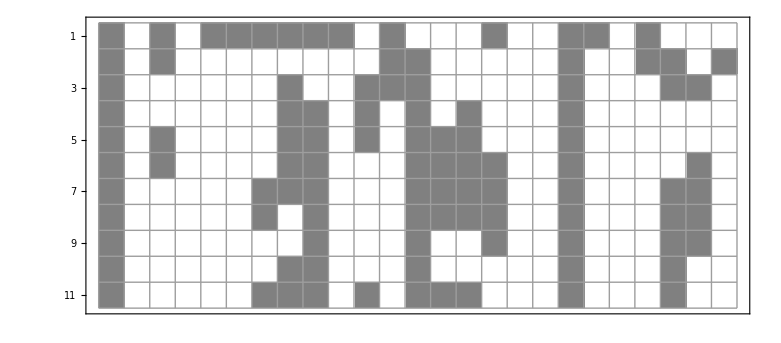

```mathematica
ArrayPlot[Values[simulation],ColorRules->{True->Gray,False->White},Mesh->True,Frame->True,FrameTicks->{{Range[1,n+1],None},{None,Thread[{Range@Length[F],Keys[F]}]}}]
```

The set of variables of the Boolean network.

```mathematica
Keys[TF]
```

{Insulin,GF,Senescence,G1S,MAPK,p16,MDM2,p53,p21,AKT,mTORC1S6K1,ATP,IRSPIK3CA,AMPK,PTEN,TSC,MYC,CDK2,RB1,E2F1,PRC,Metabolism,PP2A,FOXO,PP1C}

#### Interaction graph

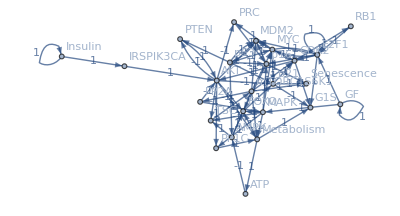

```mathematica
ig0 = InteractionGraphSimple[TF]
```

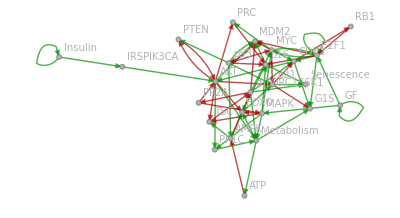

```mathematica
NiceIG[ig0]
```

```mathematica
NiceIG3D[ig0]
```

-Graphics3D-

#### Regulators

Thanks to the Regulators[] function, we can retrieve the activators and or inhibitors of a given node, even if they are defined in the logical rules.

```mathematica
Regulators[ig0, mTORC1S6K1, {-1,0,1}]
```

{AMPK,TSC}

```mathematica
Regulators[ig0, Senescence, {-1,1}]
```

{mTORC1S6K1,p16,p21}

```mathematica
Regulators[ig0, G1S, {-1}]
```

{p21}

```mathematica
Regulators[ig0, G1S, {1}]
```

{CDK2,E2F1,Metabolism}